```mathematica
f[r_,z_]=r^m g[r,z]
```

r^m g[r,z]

```mathematica
laplh=(1/r D[r D[f[r,z],r],r] - m^2/r^2 f[r,z])//FullSimplify
```

r^(-1+m) ((1+2 m) g^(1,0)[r,z]+r g^(2,0)[r,z])

```mathematica
bilaplh=(1/r D[r D[laplh,r],r] - m^2/r^2 laplh)//FullSimplify
```

r^(-3+m) (-(-1+4 m^2) (g^(1,0)[r,z]-r g^(2,0)[r,z])+2 (1+2 m) r^2 g^(3,0)[r,z]+r^3 g^(4,0)[r,z])

```mathematica
bilapl=(1/r D[r D[laplh,r],r] - m^2/r^2 laplh+D[laplh,{z,2}])//FullSimplify
```

r^(-3+m) ((1-4 m^2) g^(1,0)[r,z]+r ((r+2 m r) g^(1,2)[r,z]+(-1+4 m^2) g^(2,0)[r,z]+r (2 (1+2 m) g^(3,0)[r,z]+r (g^(2,2)[r,z]+g^(4,0)[r,z]))))

```mathematica
trilaplh=(1/r D[r D[bilaplh,r],r] - m^2/r^2 bilaplh )//FullSimplify
```

r^(-5+m) ((-1+4 m^2) ((-9+6 m) g^(1,0)[r,z]+r ((9-6 m) g^(2,0)[r,z]+r (2 (-3+m) g^(3,0)[r,z]+3 r g^(4,0)[r,z])))+3 (1+2 m) r^4 g^(5,0)[r,z]+r^5 g^(6,0)[r,z])

```mathematica
trilapl=(1/r D[r D[bilapl,r],r] - m^2/r^2 bilapl + D[bilapl,{z,2}])//FullSimplify
```

r^(-5+m) (3 (-3+2 m) (-1+2 m) (1+2 m) g^(1,0)[r,z]+r ((2-8 m^2) r g^(1,2)[r,z]+(1+2 m) r^3 g^(1,4)[r,z]-9 g^(2,0)[r,z]+6 m g^(2,0)[r,z]+36 m^2 g^(2,0)[r,z]-24 m^3 g^(2,0)[r,z]-2 r^2 g^(2,2)[r,z]+8 m^2 r^2 g^(2,2)[r,z]+r^4 g^(2,4)[r,z]+6 r g^(3,0)[r,z]-2 m r g^(3,0)[r,z]-24 m^2 r g^(3,0)[r,z]+8 m^3 r g^(3,0)[r,z]+4 r^3 g^(3,2)[r,z]+8 m r^3 g^(3,2)[r,z]-3 r^2 g^(4,0)[r,z]+12 m^2 r^2 g^(4,0)[r,z]+2 r^4 g^(4,2)[r,z]+3 r^3 g^(5,0)[r,z]+6 m r^3 g^(5,0)[r,z]+r^4 g^(6,0)[r,z]))

```mathematica
rx =√((x+1)/2)
dxdr=1/D[rx,x]
```

(√(1+x))/(√2)

2 √2 √(1+x)

```mathematica
laplh/r^m//Expand
laplhx=laplh/r^m/.{Derivative[1,0][g][r,z]->dxdr D[gg[x,z],x],Derivative[2,0][g][r,z]->dxdr D[dxdr D[gg[x,z],x],x],r->rx}//FullSimplify
```

(g^(1,0)[r,z])/r+(2 m g^(1,0)[r,z])/r+g^(2,0)[r,z]

8 ((1+m) gg^(1,0)[x,z]+(1+x) gg^(2,0)[x,z])

```mathematica
Coefficient[laplh/r^m, Derivative[2,0][g][r,z]]//Simplify
Coefficient[laplh/r^m, Derivative[1,0][g][r,z]]//Simplify
```

1

(1+2 m)/r

```mathematica
Coefficient[laplhx, Derivative[2,0][gg][x,z]]//Simplify
Coefficient[laplhx, Derivative[1,0][gg][x,z]]//Simplify
```

8 (1+x)

8 (1+m)

```mathematica
bilaplh/r^m//Expand
bilaplhx=bilaplh/r^m/.{Derivative[1,0][g][r,z]->dxdr D[gg[x,z],x],Derivative[1,2][g][r,z]->dxdr D[D[gg[x,z],{z,2}],x],
Derivative[2,0][g][r,z]->dxdr D[dxdr D[gg[x,z],x],x],
Derivative[2,2][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],
Derivative[3,0][g][r,z]->dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],Derivative[4,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],r->rx}//FullSimplify
```

(g^(1,0)[r,z])/r^3-(4 m^2 g^(1,0)[r,z])/r^3-(g^(2,0)[r,z])/r^2+(4 m^2 g^(2,0)[r,z])/r^2+(2 g^(3,0)[r,z])/r+(4 m g^(3,0)[r,z])/r+g^(4,0)[r,z]

64 ((1+m) (2+m) gg^(2,0)[x,z]+(1+x) (2 (2+m) gg^(3,0)[x,z]+(1+x) gg^(4,0)[x,z]))

```mathematica
bilapl/r^m//Expand
bilaplx=bilapl/r^m/.{Derivative[1,0][g][r,z]->dxdr D[gg[x,z],x],Derivative[1,2][g][r,z]->dxdr D[D[gg[x,z],{z,2}],x],
Derivative[2,0][g][r,z]->dxdr D[dxdr D[gg[x,z],x],x],
Derivative[2,2][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],
Derivative[3,0][g][r,z]->dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],Derivative[4,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],r->rx}//FullSimplify
```

(g^(1,0)[r,z])/r^3-(4 m^2 g^(1,0)[r,z])/r^3+(g^(1,2)[r,z])/r+(2 m g^(1,2)[r,z])/r-(g^(2,0)[r,z])/r^2+(4 m^2 g^(2,0)[r,z])/r^2+g^(2,2)[r,z]+(2 g^(3,0)[r,z])/r+(4 m g^(3,0)[r,z])/r+g^(4,0)[r,z]

8 ((1+m) gg^(1,2)[x,z]+8 (1+m) (2+m) gg^(2,0)[x,z]+(1+x) (gg^(2,2)[x,z]+16 (2+m) gg^(3,0)[x,z]+8 (1+x) gg^(4,0)[x,z]))

```mathematica
Coefficient[bilaplh/r^m, Derivative[4,0][g][r,z]]//Simplify
Coefficient[bilaplh/r^m, Derivative[3,0][g][r,z]]//Simplify
Coefficient[bilaplh/r^m, Derivative[2,0][g][r,z]]//Simplify
Coefficient[bilaplh/r^m, Derivative[1,0][g][r,z]]//Simplify
```

1

(2+4 m)/r

(-1+4 m^2)/r^2

(1-4 m^2)/r^3

```mathematica
Coefficient[bilapl/r^m, Derivative[4,0][g][r,z]]//Simplify
Coefficient[bilapl/r^m, Derivative[3,0][g][r,z]]//Simplify
Coefficient[bilapl/r^m, Derivative[2,0][g][r,z]]//Simplify
Coefficient[bilapl/r^m, Derivative[1,0][g][r,z]]//Simplify
Print["------------------------------------"]
Coefficient[bilapl/r^m, Derivative[2,2][g][r,z]]//Simplify
Coefficient[bilapl/r^m, Derivative[1,2][g][r,z]]//Simplify
```

1

(2+4 m)/r

(-1+4 m^2)/r^2

(1-4 m^2)/r^3

------------------------------------

1

(1+2 m)/r

```mathematica
Coefficient[bilaplhx, Derivative[4,0][gg][x,z]]//Simplify
Coefficient[bilaplhx, Derivative[3,0][gg][x,z]]//Simplify
Coefficient[bilaplhx, Derivative[2,0][gg][x,z]]//Simplify
Coefficient[bilaplhx, Derivative[1,0][gg][x,z]]//Simplify
```

64 (1+x)^2

128 (2+m) (1+x)

64 (1+m) (2+m)

0

```mathematica
Coefficient[bilaplx, Derivative[4,0][gg][x,z]]//Simplify
Coefficient[bilaplx, Derivative[3,0][gg][x,z]]//Simplify
Coefficient[bilaplx, Derivative[2,0][gg][x,z]]//Simplify
Coefficient[bilaplx, Derivative[1,0][gg][x,z]]//Simplify
Print["------------------------------------"]
Coefficient[bilaplx, Derivative[2,2][gg][x,z]]//Simplify
Coefficient[bilaplx, Derivative[1,2][gg][x,z]]//Simplify
```

64 (1+x)^2

128 (2+m) (1+x)

64 (1+m) (2+m)

0

------------------------------------

8 (1+x)

8 (1+m)

```mathematica
trilaplh/r^m//Expand
trilaplhx=trilaplh/r^m/.{Derivative[1,0][g][r,z]->dxdr D[gg[x,z],x],Derivative[1,2][g][r,z]->dxdr D[D[gg[x,z],{z,2}],x],
Derivative[1,4][g][r,z]->dxdr D[D[gg[x,z],{z,4}],x],
Derivative[2,0][g][r,z]->dxdr D[dxdr D[gg[x,z],x],x],
Derivative[2,2][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],
Derivative[2,4][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,4}],x],x],
Derivative[3,0][g][r,z]->dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],Derivative[3,2][g][r,z]->dxdr D[dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],x],
Derivative[4,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],
Derivative[4,2][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],x],x],
Derivative[5,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],x],
Derivative[6,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],x],x],r->rx}//Expand//Simplify
```

(9 g^(1,0)[r,z])/r^5-(6 m g^(1,0)[r,z])/r^5-(36 m^2 g^(1,0)[r,z])/r^5+(24 m^3 g^(1,0)[r,z])/r^5-(9 g^(2,0)[r,z])/r^4+(6 m g^(2,0)[r,z])/r^4+(36 m^2 g^(2,0)[r,z])/r^4-(24 m^3 g^(2,0)[r,z])/r^4+(6 g^(3,0)[r,z])/r^3-(2 m g^(3,0)[r,z])/r^3-(24 m^2 g^(3,0)[r,z])/r^3+(8 m^3 g^(3,0)[r,z])/r^3-(3 g^(4,0)[r,z])/r^2+(12 m^2 g^(4,0)[r,z])/r^2+(3 g^(5,0)[r,z])/r+(6 m g^(5,0)[r,z])/r+g^(6,0)[r,z]

512 ((6+11 m+6 m^2+m^3) gg^(3,0)[x,z]+(1+x) (3 (6+5 m+m^2) gg^(4,0)[x,z]+(1+x) (3 (3+m) gg^(5,0)[x,z]+(1+x) gg^(6,0)[x,z])))

```mathematica
trilapl/r^m//Expand
trilaplx=trilapl/r^m/.{Derivative[1,0][g][r,z]->dxdr D[gg[x,z],x],Derivative[1,2][g][r,z]->dxdr D[D[gg[x,z],{z,2}],x],
Derivative[1,4][g][r,z]->dxdr D[D[gg[x,z],{z,4}],x],
Derivative[2,0][g][r,z]->dxdr D[dxdr D[gg[x,z],x],x],
Derivative[2,2][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],
Derivative[2,4][g][r,z]->dxdr D[dxdr D[D[gg[x,z],{z,4}],x],x],
Derivative[3,0][g][r,z]->dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],Derivative[3,2][g][r,z]->dxdr D[dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],x],
Derivative[4,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],
Derivative[4,2][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[D[gg[x,z],{z,2}],x],x],x],x],
Derivative[5,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],x],
Derivative[6,0][g][r,z]->dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[dxdr D[gg[x,z],x],x],x],x],x],x],r->rx}//Expand//Simplify
```

(9 g^(1,0)[r,z])/r^5-(6 m g^(1,0)[r,z])/r^5-(36 m^2 g^(1,0)[r,z])/r^5+(24 m^3 g^(1,0)[r,z])/r^5+(2 g^(1,2)[r,z])/r^3-(8 m^2 g^(1,2)[r,z])/r^3+(g^(1,4)[r,z])/r+(2 m g^(1,4)[r,z])/r-(9 g^(2,0)[r,z])/r^4+(6 m g^(2,0)[r,z])/r^4+(36 m^2 g^(2,0)[r,z])/r^4-(24 m^3 g^(2,0)[r,z])/r^4-(2 g^(2,2)[r,z])/r^2+(8 m^2 g^(2,2)[r,z])/r^2+g^(2,4)[r,z]+(6 g^(3,0)[r,z])/r^3-(2 m g^(3,0)[r,z])/r^3-(24 m^2 g^(3,0)[r,z])/r^3+(8 m^3 g^(3,0)[r,z])/r^3+(4 g^(3,2)[r,z])/r+(8 m g^(3,2)[r,z])/r-(3 g^(4,0)[r,z])/r^2+(12 m^2 g^(4,0)[r,z])/r^2+2 g^(4,2)[r,z]+(3 g^(5,0)[r,z])/r+(6 m g^(5,0)[r,z])/r+g^(6,0)[r,z]

8 ((1+m) gg^(1,4)[x,z]+16 (2+3 m+m^2) gg^(2,2)[x,z]+gg^(2,4)[x,z]+x gg^(2,4)[x,z]+384 gg^(3,0)[x,z]+704 m gg^(3,0)[x,z]+384 m^2 gg^(3,0)[x,z]+64 m^3 gg^(3,0)[x,z]+64 gg^(3,2)[x,z]+32 m gg^(3,2)[x,z]+64 x gg^(3,2)[x,z]+32 m x gg^(3,2)[x,z]+1152 gg^(4,0)[x,z]+960 m gg^(4,0)[x,z]+192 m^2 gg^(4,0)[x,z]+1152 x gg^(4,0)[x,z]+960 m x gg^(4,0)[x,z]+192 m^2 x gg^(4,0)[x,z]+16 gg^(4,2)[x,z]+32 x gg^(4,2)[x,z]+16 x^2 gg^(4,2)[x,z]+576 gg^(5,0)[x,z]+192 m gg^(5,0)[x,z]+1152 x gg^(5,0)[x,z]+384 m x gg^(5,0)[x,z]+576 x^2 gg^(5,0)[x,z]+192 m x^2 gg^(5,0)[x,z]+64 gg^(6,0)[x,z]+192 x gg^(6,0)[x,z]+192 x^2 gg^(6,0)[x,z]+64 x^3 gg^(6,0)[x,z])

```mathematica
Coefficient[trilaplh/r^m, Derivative[6,0][g][r,z]]//FullSimplify
Coefficient[trilaplh/r^m, Derivative[5,0][g][r,z]]//FullSimplify
Coefficient[trilaplh/r^m, Derivative[4,0][g][r,z]]//FullSimplify
Coefficient[trilaplh/r^m, Derivative[3,0][g][r,z]]//FullSimplify
Coefficient[trilaplh/r^m, Derivative[2,0][g][r,z]]//FullSimplify
Coefficient[trilaplh/r^m, Derivative[1,0][g][r,z]]//FullSimplify
```

1

(3+6 m)/r

(3 (-1+4 m^2))/r^2

(2 (-3+m) (-1+2 m) (1+2 m))/r^3

(-9+6 m (1+6 m-4 m^2))/r^4

(3 (-3+2 m) (-1+2 m) (1+2 m))/r^5

```mathematica
Coefficient[trilapl/r^m, Derivative[6,0][g][r,z]]//FullSimplify
Coefficient[trilapl/r^m, Derivative[5,0][g][r,z]]//FullSimplify
Coefficient[trilapl/r^m, Derivative[4,0][g][r,z]]//FullSimplify
Coefficient[trilapl/r^m, Derivative[3,0][g][r,z]]//FullSimplify
Coefficient[trilapl/r^m, Derivative[2,0][g][r,z]]//FullSimplify
Coefficient[trilapl/r^m, Derivative[1,0][g][r,z]]//FullSimplify
Print["------------------------------------"]
Coefficient[trilapl/r^m, Derivative[4,2][g][r,z]]//Simplify
Coefficient[trilapl/r^m, Derivative[3,2][g][r,z]]//Simplify
Coefficient[trilapl/r^m, Derivative[2,4][g][r,z]]//Simplify
Coefficient[trilapl/r^m, Derivative[2,2][g][r,z]]//Simplify
Coefficient[trilapl/r^m, Derivative[1,4][g][r,z]]//Simplify
Coefficient[trilapl/r^m, Derivative[1,2][g][r,z]]//Simplify
```

1

(3+6 m)/r

(3 (-1+4 m^2))/r^2

(2 (-3+m) (-1+2 m) (1+2 m))/r^3

(-9+6 m (1+6 m-4 m^2))/r^4

(3 (-3+2 m) (-1+2 m) (1+2 m))/r^5

------------------------------------

2

(4+8 m)/r

1

(-2+8 m^2)/r^2

(1+2 m)/r

(2-8 m^2)/r^3

```mathematica
Coefficient[trilaplhx, Derivative[6,0][gg][x,z]]//Simplify
Coefficient[trilaplhx, Derivative[5,0][gg][x,z]]//Simplify
Coefficient[trilaplhx, Derivative[4,0][gg][x,z]]//Simplify//Factor
Coefficient[trilaplhx, Derivative[3,0][gg][x,z]]//Simplify//Factor
Coefficient[trilaplhx, Derivative[2,0][gg][x,z]]//Simplify
Coefficient[trilaplhx, Derivative[1,0][gg][x,z]]//Simplify
```

512 (1+x)^3

1536 (3+m) (1+x)^2

1536 (2+m) (3+m) (1+x)

512 (1+m) (2+m) (3+m)

0

0

```mathematica
Coefficient[trilaplx, Derivative[6,0][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[5,0][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[4,0][gg][x,z]]//Simplify//Factor
Coefficient[trilaplx, Derivative[3,0][gg][x,z]]//Simplify//Factor
Coefficient[trilaplx, Derivative[2,0][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[1,0][gg][x,z]]//Simplify
Print["------------------------------------"]
Coefficient[trilaplx, Derivative[2,4][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[1,4][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[4,2][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[3,2][gg][x,z]]//Simplify
Coefficient[trilaplx, Derivative[2,2][gg][x,z]]//Simplify//Factor
Coefficient[trilaplx, Derivative[1,2][gg][x,z]]//Simplify
```

512 (1+x)^3

1536 (3+m) (1+x)^2

1536 (2+m) (3+m) (1+x)

512 (1+m) (2+m) (3+m)

0

0

------------------------------------

8 (1+x)

8 (1+m)

128 (1+x)^2

256 (2+m) (1+x)

128 (1+m) (2+m)

0

```mathematica
v = Curl[{0,0,ψ[r,θ,z]},{r,θ,z},"Cylindrical"] + Curl[Curl[{0,0,ϕ[r,θ,z]},{r,θ,z},"Cylindrical"],{r,θ,z},"Cylindrical"]
```

{(ψ^(0,1,0)[r,θ,z])/r+ϕ^(1,0,1)[r,θ,z],(ϕ^(0,1,1)[r,θ,z])/r-ψ^(1,0,0)[r,θ,z],-((ϕ^(0,2,0)[r,θ,z])/r+ϕ^(1,0,0)[r,θ,z])/r-ϕ^(2,0,0)[r,θ,z]}

```mathematica
Curl[Cross[v,{0,0,1}],{r,θ,z},"Cylindrical"][[3]]//FullSimplify
```

-(ϕ^(0,2,1)[r,θ,z]+r (ϕ^(1,0,1)[r,θ,z]+r ϕ^(2,0,1)[r,θ,z]))/r^2

```mathematica
Curl[Curl[Cross[v,{0,0,1}],{r,θ,z},"Cylindrical"],{r,θ,z},"Cylindrical"][[3]]//FullSimplify
```

-(ψ^(0,2,1)[r,θ,z]+r (ψ^(1,0,1)[r,θ,z]+r ψ^(2,0,1)[r,θ,z]))/r^2

```mathematica
Curl[{0,0,τ[r,θ,z]z},{r,θ,z},"Cylindrical"][[3]]//FullSimplify
```

0

```mathematica
Curl[Curl[{0,0,τ[r,θ,z]},{r,θ,z},"Cylindrical"],{r,θ,z},"Cylindrical"][[3]]//FullSimplify
```

-(τ^(0,2,0)[r,θ,z]+r (τ^(1,0,0)[r,θ,z]+r τ^(2,0,0)[r,θ,z]))/r^2

Boundary values

```mathematica
norm[n_,l_] = If[l==0&&n==0,√(π/2),√((2n + l)(Gamma[n+l]Gamma[n+1])/(Gamma[n+1/2]Gamma[n+l+1/2]))]
```

If[l==0&&n==0,√(π/2),√(((2 n+l) (Gamma[n+l] Gamma[n+1]))/(Gamma[n+1/2] Gamma[n+l+1/2]))]

```mathematica
r^m JacobiP[n,-1/2, m-1/2,2 r^2-1]/.{r->1}
```

JacobiP[n,-1/2,-1/2+m,1]

```mathematica
d1=D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}];//Simplify
Coefficient[d1/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[d1/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

2 (m+n)

m

```mathematica
d2=D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,2}];//Simplify
Coefficient[d2/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[d2/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[d2/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

4 (m+n) (1+m+n)

2 (1+2 m) (m+n)

(-1+m) m

```mathematica
d3=D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,3}];//Simplify
Coefficient[d3/.{r->1},  JacobiP[n-3,5/2, m+5/2,1]]//Factor
Coefficient[d3/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[d3/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[d3/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

8 (m+n) (1+m+n) (2+m+n)

12 (1+m) (m+n) (1+m+n)

6 m^2 (m+n)

(-2+m) (-1+m) m

```mathematica
d4=D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,4}];//Simplify
Coefficient[d4/.{r->1},  JacobiP[n-4,7/2, m+7/2,1]]//Factor
Coefficient[d4/.{r->1},  JacobiP[n-3,5/2, m+5/2,1]]//Factor
Coefficient[d4/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[d4/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[d4/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

16 (m+n) (1+m+n) (2+m+n) (3+m+n)

16 (3+2 m) (m+n) (1+m+n) (2+m+n)

12 (1+2 m+2 m^2) (m+n) (1+m+n)

4 (-1+m) m (-1+2 m) (m+n)

(-3+m) (-2+m) (-1+m) m

```mathematica
rdiffdivr=r D[1/r r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}];//Simplify
Coefficient[rdiffdivr/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[rdiffdivr/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

2 (m+n)

-1+m

```mathematica
divrdiffr=1/r D[r r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}];//Simplify
Coefficient[divrdiffr/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[divrdiffr/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

2 (m+n)

1+m

```mathematica
laplh=(D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,2}]+1/r D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}]-m^2/r^2 r^m JacobiP[n,-1/2, m-1/2,2 r^2-1]);//Simplify
Coefficient[laplh/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[laplh/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
```

4 (m+n) (1+m+n)

4 (1+m) (m+n)

```mathematica
dlaplh=D[laplh,{r,1}];//Simplify
Coefficient[dlaplh/.{r->1},  JacobiP[n-3,5/2, m+5/2,1]]//Factor
Coefficient[dlaplh/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[dlaplh/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
```

8 (m+n) (1+m+n) (2+m+n)

4 (4+3 m) (m+n) (1+m+n)

4 m (1+m) (m+n)

```mathematica
lapl2h=(D[laplh,{r,2}]+1/r D[laplh,{r,1}]-m^2/r^2 laplh);//Simplify
Coefficient[lapl2h/.{r->1},  JacobiP[n-4,7/2, m+7/2,1]]//Factor
Coefficient[lapl2h/.{r->1},  JacobiP[n-3,5/2, m+5/2,1]]//Factor
Coefficient[lapl2h/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
```

16 (m+n) (1+m+n) (2+m+n) (3+m+n)

32 (2+m) (m+n) (1+m+n) (2+m+n)

16 (1+m) (2+m) (m+n) (1+m+n)

```mathematica
Table[lapl2h norm[n,m]/.{m->0, r->1},{n,0,10}]//N
```

{0.,0.,408.517,12255.5,125823.,755756.,3.25874×10^6,1.11983×10^7,3.26095×10^7,8.36953×10^7,1.94464×10^8}

```mathematica
rLaplh[n_,m_,r_]:=(D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,2}]+1/r D[r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}]-m^2/r^2 r^m JacobiP[n,-1/2, m-1/2,2 r^2-1]);
rescaledLaplh=rLaplh[n,m,r]/rLaplh[1,m,r];//Simplify
Coefficient[rescaledLaplh/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[rescaledLaplh/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
```

((m+n) (1+m+n))/(1+m)^2

(m+n)/(1+m)

```mathematica
diffdivrdiffr=D[1/r D[r r^m JacobiP[n,-1/2, m-1/2,2 r^2-1],{r,1}],r]//Simplify
Coefficient[diffdivrdiffr/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
Coefficient[diffdivrdiffr/.{r->1},  JacobiP[n-1,1/2, m+1/2,1]]//Factor
Coefficient[diffdivrdiffr/.{r->1},  JacobiP[n,-1/2, m-1/2,1]]//Factor
```

r^(-2+m) (4 (m+m^2+n+2 m n+n^2) r^4 JacobiP[-2+n,3/2,3/2+m,-1+2 r^2]+(1+m) (4 (m+n) r^2 JacobiP[-1+n,1/2,1/2+m,-1+2 r^2]+(-1+m) JacobiP[n,-1/2,-1/2+m,-1+2 r^2]))

4 (m+n) (1+m+n)

4 (1+m) (m+n)

(-1+m) (1+m)

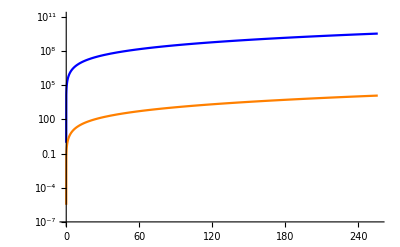

```mathematica
LogPlot[{laplh/.{r->1,m->256},rescaledLaplh/.{r->1,m->256}},{n,0,256},PlotRange->All,PlotStyle->{Blue,Orange}]
```

```mathematica
rLapl2h[n_,m_,r_]:=(D[rLaplh[n,m,r],{r,2}]+1/r D[rLaplh[n,m,r],{r,1}]-m^2/r^2 rLaplh[n,m,r])
rescaledLapl2h=rLapl2h[n,m,r]/rLapl2h[2,m,r];//Simplify
Coefficient[rescaledLapl2h/.{r->1},  JacobiP[n-4,7/2, m+7/2,1]]//Factor
Coefficient[rescaledLapl2h/.{r->1},  JacobiP[n-3,5/2, m+5/2,1]]//Factor
Coefficient[rescaledLapl2h/.{r->1},  JacobiP[n-2,3/2, m+3/2,1]]//Factor
```

((m+n) (1+m+n) (2+m+n) (3+m+n))/((1+m) (2+m)^2 (3+m))

(2 (m+n) (1+m+n) (2+m+n))/((1+m) (2+m) (3+m))

((m+n) (1+m+n))/((2+m) (3+m))

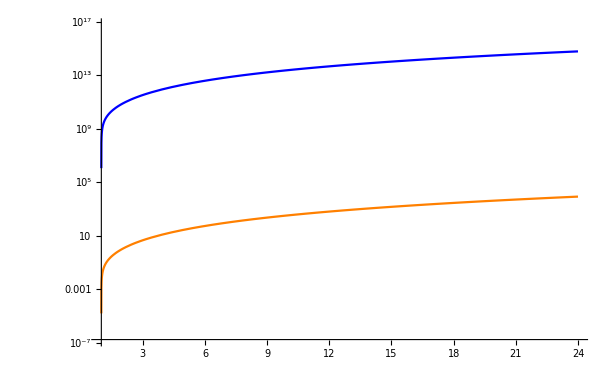

```mathematica
LogPlot[{lapl2h/.{r->1,m->256},rescaledLapl2h/.{r->1,m->256}},{n,0,24},PlotRange->All,PlotStyle->{Blue,Orange}]
```